```mathematica
Clear["Global`*"]
```

```mathematica
(*This notebook goes through some experiments to compare the "composite method" in the multivariable case, to the method that averages estimated parameters across multiple tanks. You will need to make sure you run the notebook "MAR_multitank.nb" first since it has the code for the built-in functions to do the estimates.*)
```

```mathematica
(*This generates multiple datasets (tanks) where the noise terms driving all tanks are identical. This is probably not realistic.*)

GenerateCorrelatedDatasets[A_,B_,q_,time_]:=Module[{a,b,p,noise,x0,X0,X},
p=Length[B[[1]]];
a=A[[All,1]];
b=Transpose[B];
noise=Table[RandomVariate[NormalDistribution[],p],{j,1,time+1}];
X={};
For[j=1,j≤q,j++,
x0=RandomVariate[UniformDistribution[{-1,1}],p];
X0={x0};
For[t=1,t≤time,t++;
x0=a+x0.b+noise[[t]];
X0=Join[X0,{x0}]
];
X=Join[X,{X0}]
];
X
]

(*This generates multiple datasets (tanks) where the noise terms driving all tanks are uncorrelated. This is probably more realistic.*)

GenerateUnCorrelatedDatasets[A_,B_,q_,time_]:=Module[{a,b,p,noise,x0,X0,X},
p=Length[B[[1]]];
a=A[[All,1]];
b=Transpose[B];
X={};
For[j=1,j≤q,j++,
noise=Table[RandomVariate[NormalDistribution[],p],{j,1,time+1}];
x0=RandomVariate[UniformDistribution[{-1,1}],p];
X0={x0};
For[t=1,t≤time,t++;
x0=a+x0.b+noise[[t]];
X0=Join[X0,{x0}]
];
X=Join[X,{X0}]
];
X
]


(*This generates multiple datasets (tanks) INCLUDING internally generated covariates, where the noise terms driving all tanks are uncorrelated. *)

GenerateUnCorrelatedDatasetsWithCov[A_,B_,Cc_,q_,time_]:=Module[{a,b,c,u,p,noise,x0,X0,X,cov},
p=Length[B[[1]]];
cov=Length[Cc[[1]]];
a=A[[All,1]];
b=Transpose[B];
c=Transpose[Cc];
X={};
For[j=1,j≤q,j++,
noise=Table[RandomVariate[NormalDistribution[],p],{j,1,time+1}];
u=Table[RandomVariate[NormalDistribution[],cov],{j,1,time+2}];
x0=RandomVariate[UniformDistribution[{-1,1}],p];
X0={Join[u[[1]],x0]};
For[t=1,t≤time,t++;
x0=a+x0.b+u[[t]].c+noise[[t]];
X0=Join[X0,{Join[u[[t+1]],x0]}]
];
X=Join[X,{X0}]
];
X
]
```

```mathematica
(*Experiments are below. You can change any of the main parameters (A, B, q = number of tanks,finaltime = length of timeseries). Just try to be sure that your B matrix is stable: all eigenvalues should be less than one in absolute value.*)
```

```mathematica
(*Experiment with Highly Correlated datasets*)

A={{-.2},{1.0},{.5}};
B={{.8,-.2,0},{-.1,.5,.1},{.1,0,.4}};
p=Length[B[[1]]];
q=4;
finaltime=20;

datasets=GenerateCorrelatedDatasets[A,B,q,finaltime];

CompD=CompUnConstrainedCov[datasets,0];

Mlist={};
For[i=1,i≤q,i++,
m0=CompUnConstrainedCov[{datasets[[i]]},0];
Mlist=Join[Mlist,{m0}]
]

AvgD=Mean[Mlist];


Print["Dmatrix = "MatrixForm[A],MatrixForm[B]]
Print["Comp= ",MatrixForm[CompD]," Avg = "MatrixForm[AvgD]]
Print["Eigenvalues = ",Eigenvalues[B]," -- ",Abs[Eigenvalues[CompD[[All,2;;p+1]]]]," -- ",Abs[Eigenvalues[AvgD[[All,2;;p+1]]]]]
Print["Stability = ",Det[B]^(2/p)," -- ", Det[CompD[[All,2;;p+1]]]^(2/p), " -- ",  Det[AvgD[[All,2;;p+1]]]^(2/p)]
```

Dmatrix =  (-0.2
1.
0.5)(0.8 | -0.2 | 0
-0.1 | 0.5 | 0.1
0.1 | 0 | 0.4)

Comp= (-1.54083 | 0.279209 | -0.401233 | 0.0379503
2.27216 | 0.179492 | 0.455597 | -0.392425
0.710117 | 0.143032 | -0.0508137 | 0.389144) Avg =  (-1.6171 | 0.259917 | -0.399096 | 0.0328432
2.29834 | 0.187031 | 0.454836 | -0.391727
0.706721 | 0.143664 | -0.0501289 | 0.388066)

Eigenvalues = {0.844949,0.5,0.355051} -- {0.621375,0.384076,0.384076} -- {0.615157,0.381956,0.381956}

Stability = 0.282311 -- 0.203294 -- 0.200451

```mathematica
(*Experiment with UNCorrelated datasets*)

A={{-.2},{1.0},{.5}};
B={{.8,-.2,0},{-.1,.5,.1},{.1,0,.4}};
p=Length[B[[1]]];
q=4;
finaltime=20;

datasets=GenerateUnCorrelatedDatasets[A,B,q,finaltime];

CompD=CompUnConstrainedCov[datasets,0];

Mlist={};
For[i=1,i≤q,i++,
m0=CompUnConstrainedCov[{datasets[[i]]},0];
Mlist=Join[Mlist,{m0}]
]

AvgD=Mean[Mlist];


Print["Dmatrix = "MatrixForm[A],MatrixForm[B]]
Print["Comp= ",MatrixForm[CompD]," Avg = "MatrixForm[AvgD]]
Print["Eigenvalues = ",Eigenvalues[B]," -- ",Abs[Eigenvalues[CompD[[All,2;;p+1]]]]," -- ",Abs[Eigenvalues[AvgD[[All,2;;p+1]]]]]
Print["Stability = ",Det[B]^(2/p)," -- ", Det[CompD[[All,2;;p+1]]]^(2/p), " -- ",  Det[AvgD[[All,2;;p+1]]]^(2/p)]
```

Dmatrix =  (-0.2
1.
0.5)(0.8 | -0.2 | 0
-0.1 | 0.5 | 0.1
0.1 | 0 | 0.4)

Comp= (-0.371573 | 0.783838 | -0.228215 | -0.0523021
1.29537 | 0.0312557 | 0.499437 | -0.0600206
0.454137 | 0.100509 | -0.0165668 | 0.335336) Avg =  (-0.683915 | 0.631293 | -0.336212 | -0.0695101
1.52417 | 0.030965 | 0.407041 | -0.0347099
0.651833 | 0.130003 | -0.0087896 | 0.223356)

Eigenvalues = {0.844949,0.5,0.355051} -- {0.756311,0.500835,0.361466} -- {0.567653,0.426839,0.267197}

Stability = 0.282311 -- 0.265649 -- 0.161233

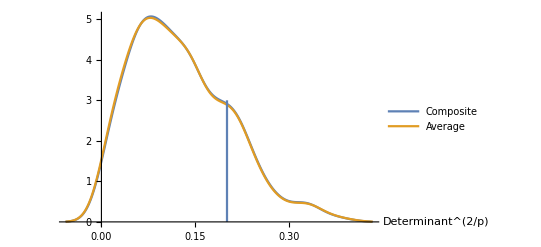

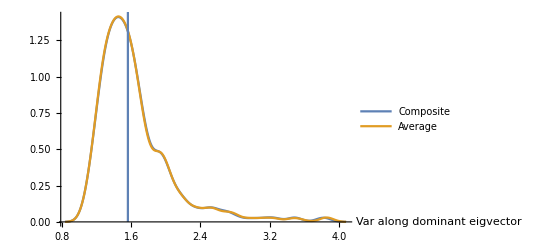

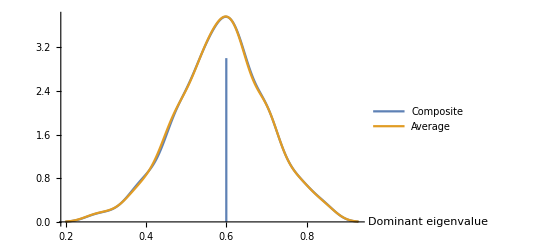

```mathematica
(*Comparison of methods for highly correlated datasets. You will notice that in this case both methods give nearly identical results. This can be understood by virtue of the fact that in this highly correlated case all tanks display nearly identical behavior and so the timeseries are basically the same across tanks.*)



A={{-.2},{1.0},{.5}};
B={{.5,-.2,0},{-.1,.5,.1},{.1,0,.4}};

(*
A={{1.0},{.5}};
B={{.4,-.2},{-.1,.5}};
*)

p=Length[B[[1]]];
q=10;
finaltime=30;

runs=500;

DetComp={};DetAvg={};
VarComp={};VarAvg={};
EigenComp={};EigenAvg={};

For[r=1,r≤runs,r++,
datasets=GenerateCorrelatedDatasets[A,B,q,finaltime];

CompD=CompUnConstrainedCov[datasets,0];
DetComp=Join[DetComp,{Det[CompD[[All,2;;p+1]]]}];
VarComp=Join[VarComp,{1/(1-(Abs[Eigenvalues[CompD[[All,2;;p+1]]]][[1]])^2)}];
EigenComp=Join[EigenComp,{Abs[Eigenvalues[CompD[[All,2;;p+1]]]][[1]]}];

Mlist={};
For[i=1,i≤q,i++,
m0=CompUnConstrainedCov[{datasets[[i]]},0];
Mlist=Join[Mlist,{m0}]
];

AvgD=Mean[Mlist];
DetAvg=Join[DetAvg,{Det[AvgD[[All,2;;p+1]]]}];
VarAvg=Join[VarAvg,{1/(1-(Abs[Eigenvalues[AvgD[[All,2;;p+1]]]][[1]])^2)}];
EigenAvg=Join[EigenAvg,{Abs[Eigenvalues[AvgD[[All,2;;p+1]]]][[1]]}]
]

Show[SmoothHistogram[{(DetComp^2)^(1/p),(DetAvg^2)^(1/p)},  PlotLegends->{"Composite","Average"},AxesLabel->{"Determinant^(2/p)"}],ParametricPlot[{(Det[B]^2)^(1/p),y},{y,0,3}]]

Show[SmoothHistogram[{VarComp,VarAvg},  PlotLegends->{"Composite","Average"},AxesLabel->{"Var along dominant eigvector"}],ParametricPlot[{1/(1-(Eigenvalues[B][[1]])^2),y},{y,0,3}]]

Show[SmoothHistogram[{EigenComp,EigenAvg},  PlotLegends->{"Composite","Average"},AxesLabel->{"Dominant eigenvalue"}],ParametricPlot[{Eigenvalues[B][[1]],y},{y,0,3}]]
```

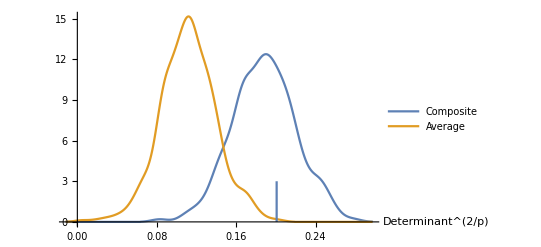

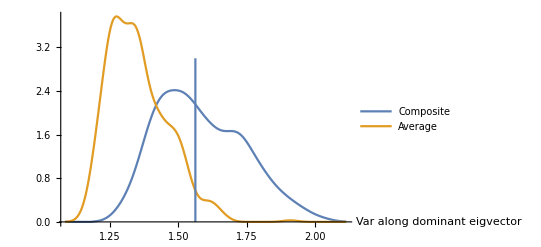

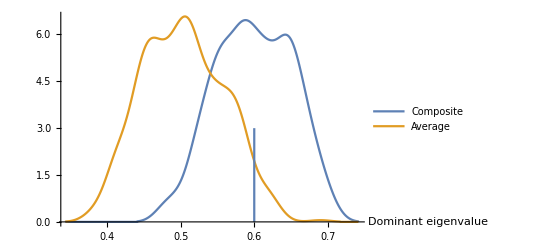

```mathematica
(*Comparison of methods for UNcorrelated datasets. Here you will see there is huge difference.*)

A={{-.2},{1.0},{.5}};
B={{.5,-.2,0},{-.1,.5,.1},{.1,0,.4}};


(*
A={{1.0},{.5}};
B={{.4,-.2},{-.1,.5}};
*)

p=Length[B[[1]]];
q=10;
finaltime=30;

runs=500;

DetComp={};DetAvg={};
VarComp={};VarAvg={};
EigenComp={};EigenAvg={};

For[r=1,r≤runs,r++,
datasets=GenerateUnCorrelatedDatasets[A,B,q,finaltime];

CompD=CompUnConstrainedCov[datasets,0];
DetComp=Join[DetComp,{Det[CompD[[All,2;;p+1]]]}];
VarComp=Join[VarComp,{1/(1-(Abs[Eigenvalues[CompD[[All,2;;p+1]]]][[1]])^2)}];
EigenComp=Join[EigenComp,{Abs[Eigenvalues[CompD[[All,2;;p+1]]]][[1]]}];

Mlist={};
For[i=1,i≤q,i++,
m0=CompUnConstrainedCov[{datasets[[i]]},0];
Mlist=Join[Mlist,{m0}]
];

AvgD=Mean[Mlist];
DetAvg=Join[DetAvg,{Det[AvgD[[All,2;;p+1]]]}];
VarAvg=Join[VarAvg,{1/(1-(Abs[Eigenvalues[AvgD[[All,2;;p+1]]]][[1]])^2)}];
EigenAvg=Join[EigenAvg,{Abs[Eigenvalues[AvgD[[All,2;;p+1]]]][[1]]}]
]

Show[SmoothHistogram[{(DetComp^2)^(1/p),(DetAvg^2)^(1/p)},  PlotLegends->{"Composite","Average"},AxesLabel->{"Determinant^(2/p)"}],ParametricPlot[{(Det[B]^2)^(1/p),y},{y,0,3}]]

Show[SmoothHistogram[{VarComp,VarAvg},  PlotLegends->{"Composite","Average"},AxesLabel->{"Var along dominant eigvector"}],ParametricPlot[{1/(1-(Eigenvalues[B][[1]])^2),y},{y,0,3}]]

Show[SmoothHistogram[{EigenComp,EigenAvg},  PlotLegends->{"Composite","Average"},AxesLabel->{"Dominant eigenvalue"}],ParametricPlot[{Eigenvalues[B][[1]],y},{y,0,3}]]
```

```mathematica
A={{-.2},{1.0},{.5}};
B={{.5,-.5,0},{-.1,.5,.1},{.1,0,.4}};
Cc={{1,2},{-1,0},{0,1}};
q=10;time=1000;

datatest=GenerateUnCorrelatedDatasetsWithCov[A,B,Cc,q,time];
Print[MatrixForm[A],MatrixForm[Cc],MatrixForm[B]]
MatrixForm[MAR[datatest,2,{{1,3},{3,2}}]]
MatrixForm[MAR[datatest,2,{}]]
```

(-0.2
1.
0.5)(1 | 2
-1 | 0
0 | 1)(0.5 | -0.5 | 0
-0.1 | 0.5 | 0.1
0.1 | 0 | 0.4)

(-0.231713 | 1.00207 | 2.00952 | 0.505492 | -0.485298 | 0
0.986691 | -0.996446 | 0.00905164 | -0.104365 | 0.502775 | 0.10824
0.516006 | -0.012962 | 1.00433 | 0.10397 | 0 | 0.393239)

(-0.230907 | 1.00206 | 2.00951 | 0.505913 | -0.484986 | -0.00107091
0.986691 | -0.996446 | 0.00905164 | -0.104365 | 0.502775 | 0.10824
0.521176 | -0.0130085 | 1.00433 | 0.102396 | -0.00393023 | 0.394763)